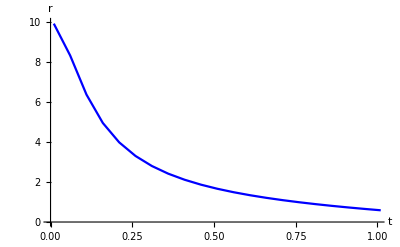

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit,M},
f[r1_,M1_,l1_]:=1-2M1/r1+r1^2/l1^2;
rm[l1_,r1_,q1_,M1_]:=NDSolveValue[{(4 l^6 M^3-4 l^6 M^2 r[t]+l^6 M r[t]^2-2 l^4 M r[t]^4+l^4 r[t]^5-3 l^2 M r[t]^6+2 l^2 r[t]^7+r[t]^9-3 l^6 M r[t]^2 r'[t]^2-3 l^4 r[t]^5 r'[t]^2-2 l^6 M q r[t] (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^6 q r[t]^2 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^4 q r[t]^4 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)-2 l^6 M r[t]^3 r''[t]+l^6 r[t]^4 r''[t]+l^4 r[t]^6 r''[t])==0/.{l->l1,q->q1,M->M1},r[0]==r1,r'[0]==0},r,{t,0.01,1.01}];
qcrit[rs_,l1_,M1_]:=rs Sqrt[f[rs,M1,l1]];
fr[l1_,r1_,t1_,q1_,M1_]:=rm[l1,r1,q1,M1][t1];
dr[l1_,r1_,t1_,q1_,M1_]:=D[rm[l1,r1,q1,M1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_,M1_]:=dr[l1,r1,t1,q1,M1]/Sqrt[-dr[l1,r1,t1,q1,M1]^2f[fr[l1,r1,t1,q1,M1],M1,l1]+f[fr[l1,r1,t1,q1,M1],M1,l1]^3];
Print[
ListLinePlot[Table[{i,fr[1,10,i,0.5 qcrit[10,2.5,0],0]//Re},{i,0.01,1.01,0.05}],PlotStyle->Blue,AxesLabel->{t,r},AxesOrigin->{0,0},PlotRange->{{0,1},{0,10}}]
]
]
```

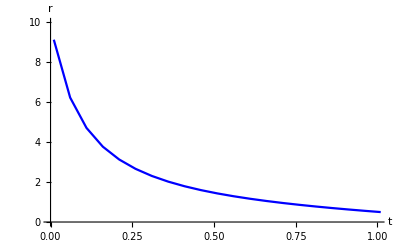

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit,M},
f[r1_,M1_,l1_]:=1-2M1/r1+r1^2/l1^2;
rm[l1_,r1_,q1_,M1_]:=NDSolveValue[{(4 l^6 M^3-4 l^6 M^2 r[t]+l^6 M r[t]^2-2 l^4 M r[t]^4+l^4 r[t]^5-3 l^2 M r[t]^6+2 l^2 r[t]^7+r[t]^9-3 l^6 M r[t]^2 r'[t]^2-3 l^4 r[t]^5 r'[t]^2-2 l^6 M q r[t] (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^6 q r[t]^2 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^4 q r[t]^4 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)-2 l^6 M r[t]^3 r''[t]+l^6 r[t]^4 r''[t]+l^4 r[t]^6 r''[t])==0/.{l->l1,q->q1,M->M1},r[0]==r1,r'[0]==0},r,{t,0.01,1.01}];
qcrit[rs_,l1_,M1_]:=rs Sqrt[f[rs,M1,l1]];
fr[l1_,r1_,t1_,q1_,M1_]:=rm[l1,r1,q1,M1][t1];
dr[l1_,r1_,t1_,q1_,M1_]:=D[rm[l1,r1,q1,M1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_,M1_]:=dr[l1,r1,t1,q1,M1]/Sqrt[-dr[l1,r1,t1,q1,M1]^2f[fr[l1,r1,t1,q1,M1],M1,l1]+f[fr[l1,r1,t1,q1,M1],M1,l1]^3];
Print[
ListLinePlot[Table[{i,fr[1,10,i,150 qcrit[10,1,0],0]//Re},{i,0.01,1.01,0.05}],PlotStyle->Blue,AxesLabel->{t,r},AxesOrigin->{0,0},PlotRange->{{0,1},{0,10}}]
]
]
```